```mathematica
(* TO DO: 1) controllare come mai non tornano i ndi; 2) controllare perché vFJ = gFJ; controllare perché non torna globalP2P3 di vFJ *)
```

In this notebook, given a network and the susceptibility values of the nodes, are computed the polarization values related to the following prejudice vectors:
			- s 		a random prejudice vector
			- s_(B_2(1)) 	  the prejudice vector that leads to the highest P_(2,3) polarization on the L_2 ball of radius 1 B_2(1)
			- s_(B_2(t))	  the prejudice vector that leads to the highest P_(2,3) polarization on the L_2 ball of radius t B_2(t), where t=1/(max_k  ((s_(B_2(1)))^(k))) 
			- s_(V_(>1))       	  the prejudice vector that leads to the highest P_(2,3) polarization on the vector spaces V_(>1) generated by the eigenvectors of H^T H corresponding to the nonnegative eigenvalues 
			- (s^heu)_(V_(>1)) 	  the prejudice vector s_(V_(>1)) computed with the developed heuristic
			- s_max_(p_(2,3)) 	  the prejudice vector that leads to the highest P_(2,3) polarization 
			-  s_(B_1(1)) 	  the prejudice vector that leads to the highest P_4 polarization on the L_1 ball of radius 1 B_1(1)
			- s_max_p_4 	  the prejudice vector that leads to the highest P_4 polarization 
The vectors computed are the polarizing vectors with positive entries. Their opposite, will give the polarizing vectors with negative entries.

## Input data

The network is given with the matrix adj, the adjacency matrix of the network. 
In this example we upload the Zachary’s Karate Club Network

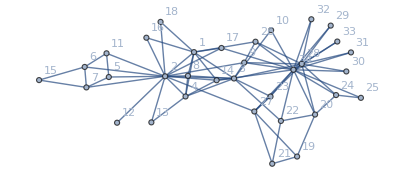

```mathematica
karate = ExampleData[{"NetworkGraph","ZacharyKarateClub"}];
adj= AdjacencyMatrix[karate];
w=N[adj/Total[adj,{2}],2]; (* influence matrix *)
numberNodes=VertexCount[karate];
AdjacencyGraph[adj,VertexLabels->"Name"]
```

The susceptibility is given with the diagonal matrix lambda, as preferred.
In this example, we set the susceptibility value of a node i equal to the PageRank centrality of the node itself (properly rescaled into the interval [0.001,0.98] to avoid degenerate cases).

```mathematica
lambdaCent[centr_]:=DiagonalMatrix[Rescale[centr,{Min[centr],Max[centr]},{0.001,0.98}]];
lambda=lambdaCent[PageRankCentrality[karate]];
```

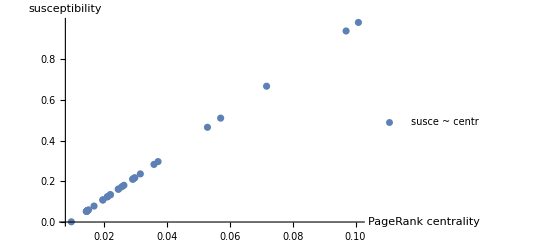

```mathematica
ListPlot[Transpose@{PageRankCentrality[karate],N[Diagonal[lambda]]},PlotRange->All,AxesLabel->{"PageRank centrality","susceptibility"},PlotLegends->{"susce ~ centr"}]
```

## Function to compute polarization

```mathematica
p1[x_]:=Norm[x-Mean[x]]^2
p2[x_]:=Norm[x]^2/Length[x]
p3[x_]:=Norm[x]^2
p4[x_]:=Norm[x,1]
ndi[x_]:=Module[{i,j,n,tot},
n=Length[w];
tot=0;
For[i=1,i<=n,i++,
For[j=i,j<=n,j++,
tot=tot+w[[i,j]]*(x[[i]]-x[[j]])^2
];
];
tot
]
gdi[x_]:=Module[{i,j,n,tot},
n=Length[w];
tot=0;
For[i=1,i<=n,i++,
For[j=i,j<=n,j++,
tot=tot+(x[[i]]-x[[j]])^2
];
];
tot
]
```

```mathematica
delta[pol_,s_]:=Module[{fun,val},
fun[x_]:=Switch[pol,
"p1",p1[x],
"p2",p2[x],
"p3",p3[x],
"p4",p4[x],
"ndi",ndi[x],
"gdi",gdi[x]];
val=fun[h.s]-fun[s];
Style[val,If[val≥0,Red,Black]]];
```

## Function to compute polarizing vectors

#### gFJ

```mathematica
getH[w_,l_]:=Module[{n,i},
n=Length[w];
i=IdentityMatrix[n];
Inverse[i-l.w].(i-l)
] (* function that compute the matrix H *)
```

```mathematica
getB[h_]:=Module[{eigen},
eigen=Eigenvectors[Transpose[h].h];
eigen[[1]]=Abs[eigen[[1]]];
eigen=#/Norm[#,2]&/@eigen;
Transpose[eigen]];(* function that compute the Perron-Frobenius vector of H *)
```

```mathematica
has1Eigen[h_]:=Module[{s0,t},
MemberQ[Eigenvalues[Transpose[h].h],1]
](* function that tests if the model has singular values equal to one *)
```

```mathematica
deltatestConditionP2P3P4[w_,lambda_]:=Module[{i,j,n,tot},
n=Length[w];
For[i=1,i<=n,i++,
tot=0;
For[j=1,j<=n,j++,
tot=tot+w[[i,j]]/(1-Diagonal[lambda][[j]]);
];
(*Print[tot,"-",1/(1-Diagonal[lambda][[i]])];*)
If[tot ≠1/(1-Diagonal[lambda][[i]]),
Return[True]];
];
False
] (* function that test if the model is polarizing with Subscript[P, 2],Subscript[P, 3],Subscript[P, 4] *)
```

```mathematica
testConditionP1GDI[h_]:=Module[{lhs,rhs},
rhs=Sqrt[1/(Length[w]*(SingularValueList[h][[1]]+1))];
lhs=Mean[Abs[Flatten[SingularValueDecomposition[h,1][[1]]]]];
If[lhs<rhs,True,False]
](* function that test if the Subscript[P, 2],Subscript[P, 3] polariziong vector is also Subscript[P, 1]/GDI-polarizing *)
```

```mathematica
getSNonDepP2P3[h_]:=Module[{},
Abs[Eigenvectors[Transpose[h].h][[1]]]
] (* funtion that finds the Subscript[P, 2],Subscript[P, 3] polarizing vector Subscript[s, Subscript[B, 2](1)] *)
```

```mathematica
getSLocalMaxPolP2P3[h_]:=Module[{s0,t},
s0=Abs[Eigenvectors[Transpose[h].h][[1]]];
t=1/Max[s0];
t*s0
](* funtion that finds the Subscript[P, 2],Subscript[P, 3] polarizing vector Subscript[s, Subscript[B, 2](t)] *)
```

```mathematica
hasOtherEigenGreater1[h_]:=Module[{s0,t},
Length[Position[Eigenvalues[Transpose[h].h][[2;;]],_?(#>1&)]]>=1
](* funtion that determines if the vector space V_(>1) is strictly larger than Subscript[B, 2](t) (and thus if the polarization can be improved) *)
```

```mathematica
getMaxAllEigen1LocalMaxPolP2P3[h_]:=Module[{n,eigenval1,eigenvec1,l,b,alpha,al,constr,max,s},
n=Length[h];
eigenval1=Eigenvalues[Transpose[h].h];
eigenval1=Extract[eigenval1,Position[(eigenval1-1),_?(#>0&)]]; (*select eigenvalus >1 *)
l=Length[eigenval1];
eigenvec1=Eigenvectors[Transpose[h].h];
eigenvec1[[1]]=Abs[eigenvec1[[1]]];
eigenvec1=eigenvec1[[1;;l]];
eigenvec1=#/Norm[#,2]&/@eigenvec1;
b=Transpose[eigenvec1];
alpha=Array[al,l];
constr=And@@(Join[Thread[b.alpha≥ConstantArray[0,n]],Thread[b.alpha<=ConstantArray[1,n]]]); (*constraints*)
max=Maximize [Total[alpha^2*(eigenval1-1)],constr,alpha];
s=b.(alpha/.max[[2]]);
{max[[1]],s}
];(* funtion that finds the polarizing vector Subscript[s, V_(>1)] and the corresponding polarization *)
```

```mathematica
testAdmittable[sCan_]:=Module[{t},
t=AllTrue[sCan,#≤1&]&&AllTrue[sCan,#≥0&];
Style[t,If[t==True,Darker[Green],Darker[Red]]]](* funtion that test if a vector is an opinion vector *)
```

```mathematica
getAllMaxPolP2P3[h_]:=Module[{n,eigen,b,alpha,al,constr,max,s},
n=Length[h];
eigen=Eigenvalues[Transpose[h].h];
b=getB[h];
alpha=Array[al,n];
constr=And@@(Join[Thread[b.alpha≥ConstantArray[0,n]],Thread[b.alpha<=ConstantArray[1,n]]]); (*constraints*)
max=Maximize [Total[alpha^2*(eigen-1)],constr,alpha];
s=b.(alpha/.max[[2]]);
{max[[1]],s,alpha}
];(* funtion that finds the global polarizing vector Subscript[Subscript[s, max], Subscript[p, 2,3]] and the corresponding polarization *)
```

```mathematica
getSLocalMaxPolP4[h_]:=Module[{i,sum},
sum=Total[h];
i=(Flatten@Position[sum,_?(#==Max[sum]&)])[[1]];
IdentityMatrix[Length[h]][[i]]
](* funtion that finds the Subscript[P, 4] polarizing vector Subscript[s, Subscript[B, 1](1)] *)
```

```mathematica
getAllMaxPolP4[h_]:=Module[{n,solution, constraints,s,sol,solS},
n=Length[h];
solution=Array[sol,n];
constraints=And@@(Join[Thread[solution≥ConstantArray[0,n]],Thread[solution<=ConstantArray[1,n]]]); 
s=Maximize[Total[h.solution]-Total[solution], constraints,solution];
solS=solution/.s[[2]];
solS
];(* funtion that finds the global polarizing vector Subscript[Subscript[s, max], Subscript[p, 4]] and the corresponding polarization *)
```

#### vFJ

```mathematica
getWHatvFJ[adj_,l_]:=Module[{n,i,d,aTilde},
n=Length[adj];
i=IdentityMatrix[n];
N[(l+adj)/Total[l+adj,{2}],2]
] (* function tha computes the influence matrix of the vFJ model *)
getHvFJ[adj_,l_]:=Module[{n,i,d,aTilde,la},
n=Length[adj];
i=IdentityMatrix[n];
d=DiagonalMatrix[Total[adj]];
la=Diagonal[l];
aTilde=d*DiagonalMatrix[(1-la)/la];
Inverse[aTilde+d-adj].aTilde
](* function tha computes the matrix Subscript[H, v] of the vFJ model *)
```

```mathematica
testConditionP2P3P4vFJ[adj_,l_]:=Module[{i,j,n,tot,d,aTilde,wHat},
n=Length[adj];
n=Length[adj];
i=IdentityMatrix[n];
aTilde=DiagonalMatrix[Diagonal[l]^(-1)];
wHat=aTilde+adj;
For[i=1,i<=n,i++,
tot=0;
For[j=1,j<=n,j++,
If[j≠i,tot=tot+wHat[[j,i]]/wHat[[j,j]]];
];
If[tot ≠Total[wHat[[i,;;]]]/(wHat[[i,i]]),
Return[True]];
];
False
];(* function that test if the model is polarizing with Subscript[P, 2],Subscript[P, 3],Subscript[P, 4] *)
```

## Compute the polarization values of the network

```mathematica
folder="insertfolderpath";(* specify the folder of  heuristic_SoBigData++.nb *)
```

## gFJ

Gets the vectors and the corresponding polarization values

```mathematica
h=getH[w,lambda];
s=RandomVariate[UniformDistribution[{0,1}],numberNodes]; (* a generic vector that one wants to test *)
```

```mathematica
Print["Is the gFJ able to polarise in P2,P3,P4? ",deltatestConditionP2P3P4[w,lambda]] (* say if the vector is polarizing *)


sNonDep=getSNonDepP2P3[h];
Print["Calculated s_B_2 "];
Print["Does this vector polarise also in P1/GDI? ",testConditionP1GDI[h]]
sLocalMax=getSLocalMaxPolP2P3[h];
Print["Calculated s_B_2 "];
Print["Can be improved in V_(>1)? ",hasOtherEigenGreater1[h]]
sAllLocal=getMaxAllEigen1LocalMaxPolP2P3[h][[2]];
Print["Calculated s_(V_(>1)) "];
Print["Is the solution in V_(>1) fesible? "testAdmittable[sAllLocal]]
Print["Calculate the solution (s^heu)_(V_(>1)) with heuristic... "];
NotebookEvaluate[folder<>"heuristic_SoBigData++.nb"];
sHeuGFJ=sMax;
Print["Has other points that leads to the covex optimum? ",has1Eigen[h]]
sGlobalP2P3=getAllMaxPolP2P3[h][[2]];
Print["Calculated s_max_(p_(2, 3)) "];
```

Is the gFJ able to polarise in P2,P3,P4? True

Calculated s_B_2

Does this vector polarise also in P1/GDI? False

Calculated s_B_2

Can be improved in V_(>1)? True

Calculated s_(V_(>1))

Is the solution in V_(>1) fesible?  False

Calculate the solution (s^heu)_(V_(>1)) with heuristic...

***Optimize component eigenvector: 2***

Search the solutions with β<0

m is positive? False

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

cannot improve anymore

cannot improve anymore

???is correct???True

Good opinion vectors? True

Polarization improved? True

Search the solutions with β>0

m is positive? True

cannot improve anymore

Good opinion vectors? True

Polarization improved? False

Has other points that leads to the covex optimum? False

Calculated s_max_(p_(2, 3))

```mathematica
sLocalMaxP4=getSLocalMaxPolP4[h];
Print["Calculated s_B_1 "];
sGlobalP4=getAllMaxPolP4[h];
Print["Calculated s_max_P_4 "];
```

Calculated s_B_1

Calculated s_max_P_4

The grid of the vectors computed with their polarization values:

```mathematica
allPolGFJ=Grid[{{"","p1","p2","p3","p4","NDI","GDI"},
{"s",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@s,
{"s_B_2",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sNonDep,
{"s_B_2",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sLocalMax,
{"s_(V_(>1))",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sAllLocal,
{"(s^heu)_(V_(>1))",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sHeuGFJ,
{"s_max_(p_(2, 3)) ",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sGlobalP2P3,
{"s_B_1",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sLocalMaxP4,
{"s_max_P_4 ",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sGlobalP4
},Frame->All];
```

```mathematica
allPolGFJ
```

| p1 | p2 | p3 | p4 | NDI | GDI
s | -1.13159 | -0.0198864 | -0.676136 | 0.429408 | -2.01859 | -38.4741
s_B_2 | -0.0640176 | 0.00223829 | 0.0761017 | 0.417889 | -0.278958 | -2.1766
s_B_2 | -1.1452 | 0.0400403 | 1.36137 | 1.76747 | -4.99023 | -38.9368
s_(V_(>1)) | -1.18474 | 0.0413065 | 1.40442 | 1.79545 | -5.05462 | -40.2813
(s^heu)_(V_(>1)) | -1.18474 | 0.0413065 | 1.40442 | 1.79545 | -5.05462 | -40.2813
s_max_(p_(2, 3))  | -1.80829 | 0.0603107 | 2.05056 | 2.05055 | -6.47256 | -61.4818
s_B_1 | -0.194999 | -0.005446 | -0.185164 | 0.155156 | -0.127648 | -6.62996
s_max_P_4  | -3.5712 | 0.0341295 | 1.1604 | 2.6524 | -8.84311 | -121.421

## vFJ

Gets the vectors and the corresponding polarization values

```mathematica
w=getWHatvFJ[adj,lambda];
h=getHvFJ[adj,lambda];
s=RandomVariate[UniformDistribution[{0,1}],numberNodes]; (* a generic vector that one wants to test *)
```

```mathematica
Print["Is the vFJ able to polarise in P2,P3,P4? ",deltatestConditionP2P3P4[w,lambda]] (* say if the vector is polarizing *)
```

Is the vFJ able to polarise in P2,P3,P4? True

```mathematica
sNonDepVFJ=getSNonDepP2P3[h];
Print["Calculated s_B_2 "];
Print["Does this vector polarise also in P1/GDI? ",testConditionP1GDI[h]]
sLocalMaxVFJ=getSLocalMaxPolP2P3[h];
Print["Calculated s_B_2 "];
Print["Can be improved in V_(>1)? ",hasOtherEigenGreater1[h]]
sAllLocalVFJ=getMaxAllEigen1LocalMaxPolP2P3[h][[2]];
Print["Calculated s_(V_(>1)) "];
Print["Is the solution in V_(>1) fesible? "testAdmittable[sAllLocalVFJ]]
Print["Calculate the solution (s^heu)_(V_(>1)) with heuristic... "];
NotebookEvaluate[folder<>"heuristic_SoBigData++.nb"];
sHeuVFJ=sMax;

sGlobalP2P3VFJ=getSLocalMaxPolP2P3[h];
Print["Calculated s_max_(p_(2, 3)) "];
```

Calculated s_B_2

Does this vector polarise also in P1/GDI? False

Calculated s_B_2

Can be improved in V_(>1)? True

Calculated s_(V_(>1))

Is the solution in V_(>1) fesible?  False

Calculate the solution (s^heu)_(V_(>1)) with heuristic...

***Optimize component eigenvector: 2***

Search the solutions with β<0

m is positive? False

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

cannot improve anymore

cannot improve anymore

???is correct???True

Good opinion vectors? True

Polarization improved? True

Search the solutions with β>0

m is positive? True

cannot improve anymore

Good opinion vectors? True

Polarization improved? False

Calculated s_max_(p_(2, 3))

```mathematica
sLocalMaxP4VFJ=getSLocalMaxPolP4[h];
Print["Calculated s_B_1 "];
sGlobalP4VFJ=getAllMaxPolP4[h];
Print["Calculated s_max_P_4 "];
```

Calculated s_B_1

Calculated s_max_P_4

The grid of the vectors computed with their polarization values:

```mathematica
allPolVFJ=Grid[{{"","p1","p2","p3","p4","NDI","GDI"},
{"s",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@s,
{"s_B_2",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sNonDepVFJ,
{"s_B_2",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sLocalMaxVFJ,
{"s_(V_(>1))",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sAllLocalVFJ,
{"(s^heu)_(V_(>1))",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sHeuVFJ,
{"s_max_(p_(2, 3)) ",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sGlobalP2P3VFJ,
{"s_B_1",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sLocalMaxP4VFJ,
{"s_max_P_4 ",delta["p1",#],delta["p2",#],delta["p3",#],delta["p4",#],delta["ndi",#],delta["gdi",#]}&@sGlobalP4VFJ
},Frame->All];
```

```mathematica
allPolVFJ
```

| p1 | p2 | p3 | p4 | NDI | GDI
s | -0.647359 | -0.0186081 | -0.632675 | 0.0137911 | -0.538556 | -22.0102
s_B_2 | -0.0640176 | 0.00223829 | 0.0761017 | 0.417889 | -0.269675 | -2.1766
s_B_2 | -1.1452 | 0.0400403 | 1.36137 | 1.76747 | -4.82416 | -38.9368
s_(V_(>1)) | -1.18474 | 0.0413065 | 1.40442 | 1.79545 | -4.88574 | -40.2813
(s^heu)_(V_(>1)) | -1.18474 | 0.0413065 | 1.40442 | 1.79545 | -4.88574 | -40.2813
s_max_(p_(2, 3))  | -1.1452 | 0.0400403 | 1.36137 | 1.76747 | -4.82416 | -38.9368
s_B_1 | -0.194999 | -0.005446 | -0.185164 | 0.155156 | -0.122388 | -6.62996
s_max_P_4  | -3.5712 | 0.0341295 | 1.1604 | 2.6524 | -8.50646 | -121.421